# Example

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/PS1/code"];
```

## Question 2

### (iii)

Maximum safe to spend

```mathematica
maxC[μ_,T_]:=(μ*w0)/(1-ⅇ^(-μ*T))
```

Parameters

```mathematica
w0=1;
```

Plot household maximum safe to spend and wealth

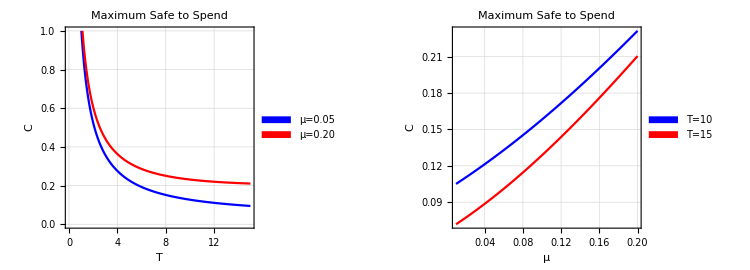

```mathematica
maxSafeSpend1= Plot[{maxC[0.05,T],maxC[0.20,T]},{T,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"T","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
maxSafeSpend2= Plot[{maxC[μ,10],maxC[μ,15]},{μ,0.01,0.20},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"T=10","T=15"}],{0.13,0.88}],
FrameLabel->{"μ","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0.01,0.20},{Min[maxC[0.01,10],maxC[0.01,15]],Max[maxC[0.20,10],maxC[0.20,15]]}}];
maxSafeSpend=GraphicsGrid[{{maxSafeSpend1,maxSafeSpend2}},ImageSize->{750,270}]
Export["images/max-safe-spend.jpeg",maxSafeSpend];
```

#### (iv)

Clear variables

```mathematica
Clear["Global`*"]
```

ODE wealth - consumption

```mathematica
DSolve[{a'[t]+(2*(ψ-1)*μ-δ*ψ)*a[t]+2^(1-ψ)==0,a[T]==2^-ψ},a[t],t]//FullSimplify
```

{{a[t]→(2^-ψ (-2+ⅇ^(-((t-T) (2 μ (-1+ψ)-δ ψ))) (2+2 μ (-1+ψ)-δ ψ)))/(2 μ (-1+ψ)-δ ψ)}}

### (v)

Clear variables

```mathematica
Clear["Global`*"]
```

ODE consumption

```mathematica
DSolve[{μ-1/ψ*1/c[t]*c'[t]-δ==0},c[t],t]//Simplify
```

{{c[t]→ⅇ^(t (-δ+μ) ψ) C[1]}}

ODE wealth

```mathematica
DSolve[{w'[t]==w[t]*μ-ⅇ^(t *(μ - δ)* ψ)* C[1]},w[t],t]//Simplify
```

{{w[t]→ⅇ^(t μ) ((ⅇ^(t (μ (-1+ψ)-δ ψ)) C[1])/(μ+δ ψ-μ ψ)+C[2])}}

### (vi)

Consumption savings

```mathematica
cS[ψ_,δ_,μ_]:=(ψ*δ+(1-ψ)*μ)/(1-(ψ*δ+(1-ψ)*μ))
```

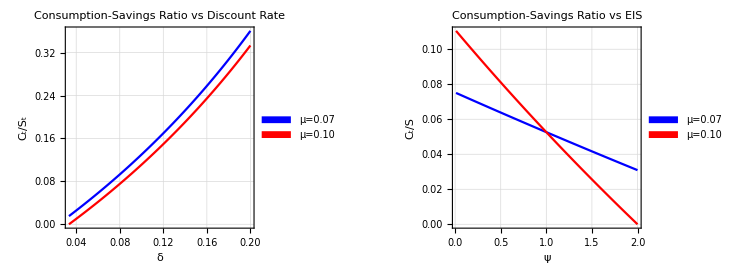

```mathematica
cSδ= Plot[{cS[1.5,δ,0.07],cS[1.5,δ,0.10]},{δ,(0.10*(1.5-1))/1.5,0.20},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Savings Ratio vs Discount Rate",
PlotLegends->Placed[SwatchLegend[{"μ=0.07","μ=0.10"}],{0.12,0.88}],
FrameLabel->{"δ","C_t/S_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{(0.10*(1.5-1))/1.5,0.20},{0,cS[1.5,0.20,0.07]}}];
cSψ= Plot[{cS[ψ,0.05,0.07],cS[ψ,0.05,0.10]},{ψ,0.01,0.10/(0.10-0.05)},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Savings Ratio vs EIS",
PlotLegends->Placed[SwatchLegend[{"μ=0.07","μ=0.10"}],{0.87,0.88}],
FrameLabel->{"ψ","C_t/S"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0.01,0.10/(0.10-0.05)},{0,cS[0.01,0.05,0.10]}}];
consumptionSavings=GraphicsGrid[{{cSδ,cSψ}},ImageSize->{750,270}]
Export["images/consumption-savings.jpeg",consumptionSavings];
```

## Question 3

Clear variables

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{μ'[t]==κ*(θ-μ[t]),μ[0]==μ0},μ[t],t]//FullSimplify
```

{{μ[t]→θ+ⅇ^(-t κ) (-θ+μ0)}}

```mathematica
DSolve[{w'[t]==w[t]*μ[t]-c[t],w[0]==w0},w[t],t]
```

{{w[t]→ⅇ^(μ[K[1]]K[1]0t) (w0+-ⅇ^(-μ[K[1]]K[1]0K[2]) c[K[2]]K[2]0t)}}